```mathematica
Needs["VariationalMethods`"]
Quit;
ClearAll;
```

```mathematica
Action=Sqrt[r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^4/rmin^2==r[x]^2+2 r'[x] v'[x]-(-m[v[x]]+r[x]^2) v'[x]^2},m[v[x]]]] ;(*We can eliminate one of the two EL equaitons using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

```mathematica
a=1/3; (*Parameter which controls the speed of the perturbation*)
Subscript[m, 0]=1; (*final value of mass function*)
m[v_]:=Subscript[m, 0](Tanh[v/a]+1)/2; (*define the mass function*)
t=6; (*Inital field theory time on boundary*)
rmax=100;
xmax=100;
```

rmin= 0.1

b= 0.89099

vmin= -6.64784

ℓ/2= 11.931

x @ vmin 11.931

x @ rmin 11.931

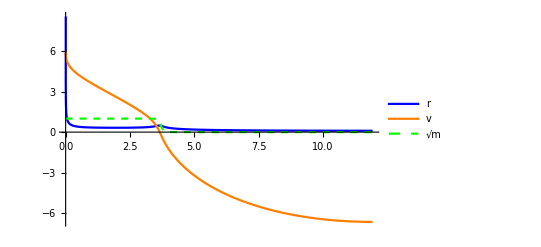

```mathematica
r0=0.1; (*Minimum value of r*)
Eqn1=r0^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2)-r[x]^4; (*the two equations of motion eqns 4.6, 4.7*)
Eqn2=r[x]^2-r[x]^2 v'[x]^2-r[x]v''[x]+2v'[x]r'[x];
x0=r0/(rmax)^2; (*x0 must be adjusted wrt to r0 and rmax *)
b=0.89099; (*integration const b, b nonzero for r0<1.0, i.e. inside the Vaidya geometry*)
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax+b/(2 rmax^2),v'[x0]==-rmax/r0+b/r0},{r,v},{x,x0,xmax}];
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]]; (*x=ℓ/2 when r'=v'=0, r[x]=r0,v[x]=v0*)
Print["rmin= ",rmin=First[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["b= ",b]
Print["vmin= ",vmin=First[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["ℓ/2= ",ℓ/2]
Print["x @ vmin ",x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["x @ rmin ",x/.Last[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
ab=Plot[{Evaluate[r[x]/.Sol],Evaluate[v[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,Orange,{Dashed,Green}},PlotLegends->{"r","v","√m"}]
```

```mathematica
ac=ParametricPlot3D[{Evaluate[{x,v[x],r[x]}/.Sol]},{x,x0,ℓ/2},AxesLabel->{"x","v","r"},PlotRange->{{x0,ℓ/2},{-8,t},{0.0,2.0}}]
```

-Graphics3D-

```mathematica
pq=ParametricPlot3D[Evaluate[{y,v[x],Sqrt[m[v[x]]]}/.Sol],{x,x0,ℓ/2},{y,x0,ℓ/2}]
```

-Graphics3D-

```mathematica
f=Show[{ac,pq},AspectRatio->1/2]
```

-Graphics3D-

```mathematica
Show[f,pq]
```

-Graphics3D-

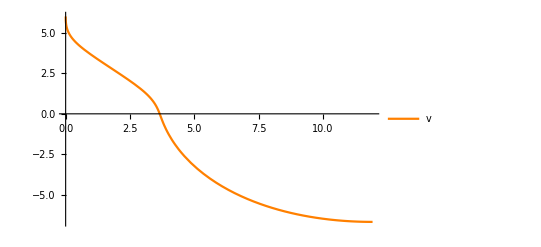

```mathematica
Plot[{Evaluate[v[x]/.Sol]},{x,x0,ℓ/2},PlotRange->All,PlotStyle->{Orange},PlotLegends->{"v"},PlotRange->All]
```

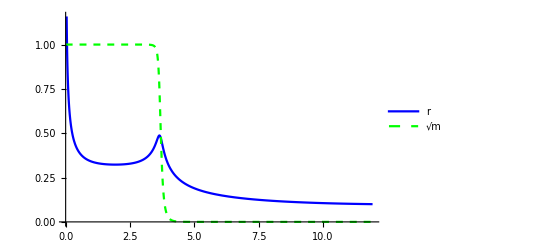

```mathematica
Plot[{Evaluate[r[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,{Dashed,Green}},PlotLegends->{"r","√m"}]
```